# Compact Rotation Representation

Consider the compact representation
	Q=I-V.T^-1.Vᵀ
where the m×r matrix Vis tall and skinny i.e m>>r.  Q is orthogonal if 
	Qᵀ.Q=I 
or equivalently 
	V.(T^-1+(T^-1)^ᵀ).Vᵀ=V.((T^-1)^ᵀ.V.Vᵀ.(T^-1)).Vᵀ
since V is full rank  
	T^-1+(T^-1)^ᵀ=(T^-1)^ᵀ.Vᵀ.V.(T^-1)
Multiplying by T gives and Tᵀ gives
(A)	 Tᵀ+T=Vᵀ.V
Note V does not need to be orthogonal and T does not need to be symmetric.

## T Symmetric

If T is symmetric we have T=0.5Vᵀ.V and 
	Q=I-2 V.(Vᵀ.V)^-1.Vᵀ
which is simply the block H rotation associated with the block projection.

### Zeroing

It is possible to chose V to zero portions of a TS block matrix Y.
	Q.Y=(I-2 V.T^-1.Vᵀ).Y=Y-2V.T^-1.Vᵀ.Y
I am given Y and I get to pick V and T consistent with Tᵀ+T=Vᵀ.V.

Assume Y is m×r and V is m×s.  Then T is s×s and equation (A) is a set of (s-1)s/2 constraints.

#### Block Householder

A block householder computation has Y and V the same shape i.e. r=s and chooses V to zero the bottom portion of Y i.e 
	(Y_1
Y_2)-2(V_1
V_2).T^-1.(V_1^ᵀ | V_2^ᵀ).(Y_1
Y_2)=(X_1
0) 
for some r×r matrix X_1. The condition simplifies to
	(Y_1
Y_2)-2(V_1
V_2).T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.Y_2)=(X_1
0)
The bottom section gives
	Y_2-2V_2.T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.Y_2)=0
So V_2=Y_2.G^-1 for some r×r matrix G. Alternatively Y_2=V_2.G and substituting gives
	Y_2=2Y_2.G^-1.T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.V_2.G)
or equivalently
	V_2=2V_2.T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.V_2.G)	
Assume V_2 is full rank then (multiplying by V_2^†) gives
	I_r=2.T^-1(V_1^ᵀ.Y_1+V_2^ᵀ.V_2.G)
Since (A) gives 
	V_1^ᵀ.V_1+V_2^ᵀ.V_2=T+Tᵀ
I have 
	I_r=2.T^-1(V_1^ᵀ.Y_1+((T+Tᵀ)-V_1^ᵀ.V_1).G)
or 
	T=2(V_1^ᵀ.(Y_1-V_1.G)+T.G+Tᵀ.G)

# CholeskyQR and

The objective of this program is two-fold. It is to first use a user programed ODE solver that can use multiple RK schemes to solve an ODE numerically. In this program the Rossler system is also converted to Cylindrical coordinates and the solutions are computed and analyzed. The solution curves are also looked at one dimension at a time to try and get an idea of what is going on. There are also some comparisons happening between the cylindrical and Cartesian coordinate graphs. There are some interesting traits when this is done.

```mathematica
(*This is the matrix that represents all of the coeficents for the Dormand-Prince 4/5 RK scheme*)
DP = {
{1/5,0,0,0,0,0},
{3/40,9/40,0,0,0,0},
{44/45,-56/15,32/9,0,0,0},
{19372/6561,−25360/2187,64448/6561,−212/729,0,0},{9017/3168,−355/33,46732/5247,49/176,−5103/18656,0},{35/384,0,500/1113,125/192,−2187/6784,11/84}
};
```

```mathematica
(* Now we can create our ode solver*)(*This is essentially the same as what we built in class except it uses the matrix for the coeficents*)
ODEStep[f_,RK_,Tol_][{y_,t_,k1_,h_}]:=Module[
{k2,k3,k4,k5,k6,k7,yNew,ErrorEst,hNew},
k2=f[y+h*RK[[1,1]]*k1];
k3=f[y+h*(RK[[2,1]]*k1+RK⟦2,2⟧*k2)];
k4=f[y+h*(RK[[3,1]]*k1+RK⟦3,2⟧*k2+RK⟦3,3⟧*k3)];
k5=f[y+h*(RK[[4,1]]*k1+RK⟦4,2⟧*k2+RK⟦4,3⟧*k3+RK[[4,4]]*k4)];
k6=f[y+h*(RK[[5,1]]*k1+RK⟦5,2⟧*k2+RK⟦5,3⟧*k3+RK[[5,4]]*k4+RK[[5,5]]*k5)];
yNew=y+h*(RK[[6,1]]*k1+RK⟦6,2⟧*k2+RK⟦6,3⟧*k3+RK[[6,4]]*k4+RK[[6,5]]*k5+RK[[6,6]]*k6);
k7=f[yNew];
(*This is the same error estimate tool that we used before*)
ErrorEst=h*Norm[(5179/57600-35/384)*k1+(7571/16695-500/1113)*k3+(393/640-125/192)*k4+(−92097/339200+2187/6784)*k5+(187/2100-11/84)*k6+(1/40)*k7];
If[ErrorEst>Tol,
{y,t,k1,0.5h},
hNew=0.9*(Tol/ErrorEst)^(1/6)*h;
(*{yNew,t+h,k7,hNew} is the function output*)
{yNew,t+h,k7,hNew}
]
]
```

```mathematica
(* First the function "g" must be defined this is the function we will run the solver on. This is the rossler system in carteasan coordinates*)
{a,b,c}={0.2,0.2,5.7};
g[{x_,y_,z_}]:={-y-z,x+a*y,b+z*(x-c)}
{y0,t0}={{0.2,0.4,13.4},0};
(* Now all of the solver initial condtions and values must be defined*)
{h0,MaxIter,Tol}={0.0001,1000,0.00001};
k1=g[y0];(* k1 is the first step passed into the fsal scheme*)
Dataxyz=NestList[ODEStep[g,DP,Tol],{y0,t0,k1,h0},MaxIter];
ListPointPlot3D[Dataxyz[[All,1]],PlotRange->All]
```

-Graphics3D-

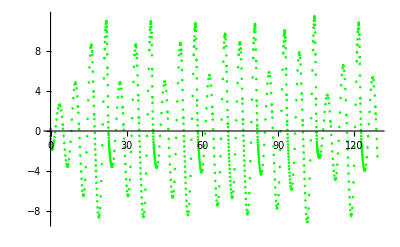

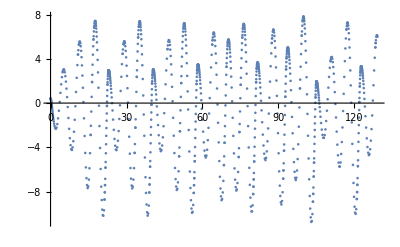

```mathematica
(*Here is some matrix calculations that allow me to isolate the points with respect to time. After doing that I can graph all of the output variables individually with respect to t.*)
Pts=Dataxyz[[All,1]];
T=Dataxyz[[All,2]];
xPts=Pts[[All,1]];
yPts=Pts[[All,2]];
zPts=Pts[[All,3]];
xPtsT={T,xPts}ᵀ;
yPtsT={T,yPts}ᵀ;
zPtsT={T,zPts}ᵀ;
xPlot=ListPlot[xPtsT,PlotStyle->Green]
yPlot=ListPlot[yPtsT]
zPlot=ListPlot[zPtsT];
```

```mathematica
(* First the function "f" must be defined this is the function we will run the solver on. This is the version of the funcion in cylindrical coordinates.*)
{a,b,c}={0.2,0.2,5.7};
f[{r_,θ_,z_}]:={((-z/Cos[θ])-a*r*Tan[θ]^2)/(1-Tan[θ]^2),1-Tan[θ]*(a+((((-z/Cos[θ])-a*r*Tan[θ]^2)/(1-Tan[θ]^2))/r)),
b+z*(r*Cos[θ]-c)}
f[{x_,y_,z_}]:={-y-z,x+a*y,b+z*(x-c)}
{y0,t0}={{0.447213595499958,1.1071487177940906,13.4},0};
(* Now all of the solver initial condtions and values must be defined*)
{h0,MaxIter,Tol}={0.0001,1000,0.00001};
k1=f[y0];(* k1 is the first step passed into the fsal scheme*)
Data=NestList[ODEStep[f,DP,Tol],{y0,t0,k1,h0},MaxIter];
ListPointPlot3D[Data[[All,1]],PlotRange->All]
```

-Graphics3D-

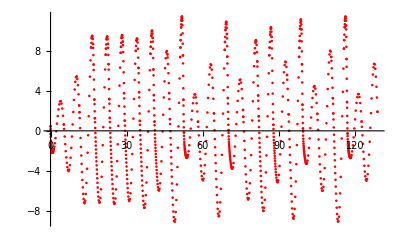

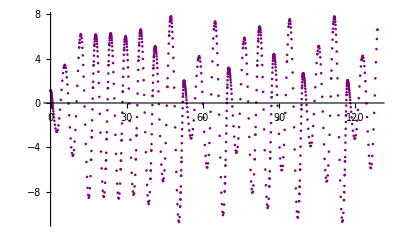

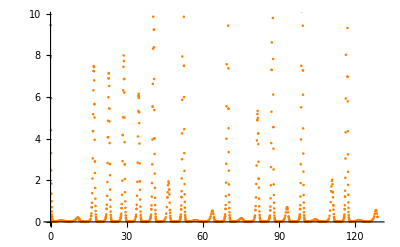

```mathematica
(*Here is some matrix calculations that allow me to isolate the points with respect to time. After doing that I can graph all of the output variables individually with respect to t.*)
Pts=Data[[All,1]];
T=Data[[All,2]];
rPts=Pts[[All,1]];
θPts=Pts[[All,2]];
zPts=Pts[[All,3]];
rPtsT={T,rPts}ᵀ;
θPtsT={T,θPts}ᵀ;
zPtsT={T,zPts}ᵀ;
rPlot=ListPlot[rPtsT,PlotStyle->Red]
θPlot=ListPlot[θPtsT,PlotStyle->Purple]
zPlot=ListPlot[zPtsT,PlotStyle->Orange]
```

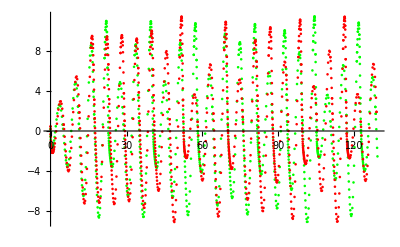

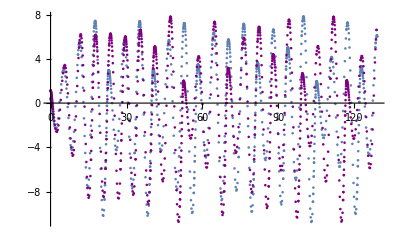

```mathematica
Show[xPlot,rPlot]
Show[yPlot,θPlot]
(* The θ plot is the one that is confusing me. I think it should be some sort of discontinuous curve that goes from 0 to 2Π*)
Show[zPlot];
```

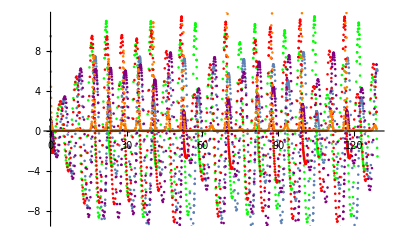

```mathematica
Show[xPlot,yPlot,rPlot,θPlot,zPlot](*xPlot->Green,yPlot->Blue,rPlot->Red,θPlot->Purple,zPlot->Orange*)(*{x,r} and {y,θ} are interestingly similar, it makes me wonder if I did something wrong*)
```